## Using Mathematica for calculus

Mathematica is what Wolfram Alpha is based on
(You may be familiar from Math 1A...)

There is very powerful built-in differentiation and integration of expressions:

```mathematica
D[Sqrt[x]Tanh[Sin[x]],x]
```

√x Cos[x] Sech[Sin[x]]^2+Tanh[Sin[x]]/(2 √x)

Integrate can be used to compute indefinite integrals

```mathematica
Integrate[Sqrt[x]Cos[x]Sech[Sin[x]]^2+Tanh[Sin[x]]/2/Sqrt[x],x]
```

√x Tanh[Sin[x]]

Providing bounds of integration in the form of a list (just like in plotting) can be used to compute definite integrals

```mathematica
Integrate[Sqrt[x]Cos[x]Sech[Sin[x]]^2+Tanh[Sin[x]]/2/Sqrt[x],{x,0,Pi/2}]
```

√(π/2) Tanh[1]

Numerical (approximate results) can be obtained using the N function

```mathematica
N[Sqrt[Pi/2] Tanh[1]]
```

0.954517

```mathematica
N[Sqrt[Pi/2] Tanh[1],30]
```

0.95451672255622602845083958305

If we want to be fancy, we can use mathematical notation in our code:

```mathematica
N[√(π/2)Tanh[1],30]
```

0.95451672255622602845083958305

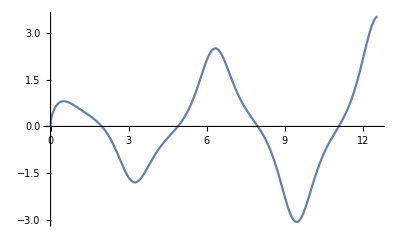

```mathematica
Plot[Sqrt[x]Cos[x]Sech[Sin[x]]^2+Tanh[Sin[x]]/2/Sqrt[x],{x,0,4Pi}]
```

## More calculus and series

Mathematica can easily compute partial and repeated derivatives

```mathematica
D[x^n,x]
```

n x^(-1+n)

```mathematica
D[x^n,{x,2}]
```

(-1+n) n x^(-2+n)

```mathematica
D[x^n,{x,5}]
```

(-4+n) (-3+n) (-2+n) (-1+n) n x^(-5+n)

```mathematica
D[Sin[x]Cos[y],{{x,y}}]
```

{Cos[x] Cos[y],-Sin[x] Sin[y]}

Finite and infinite sums can be computed using Sum

```mathematica
Sum[x^i/i,{i,1,10}]
```

x+x^2/2+x^3/3+x^4/4+x^5/5+x^6/6+x^7/7+x^8/8+x^9/9+x^10/10

```mathematica
Sum[1/i^4,{i,1,Infinity}]
```

π^4/90

```mathematica
Sum[1/2^i,{i,0,Infinity}]
```

2

```mathematica
Product[(x+i),{i,1,5}]
```

(1+x) (2+x) (3+x) (4+x) (5+x)

## Differential equations

Mathematica can find analytical solutions to many differential equations, both initial value problems and boundary value problems

The function DSolve looks for solutions to differential equations

```mathematica
DSolve[y'[x]==a y[x]+1,y,x]
```

{{y→Function[{x},-1/a+ⅇ^(a x) C[1]]}}

We did not specify an initial condition, so the solution has a constant. Specifying the initial condition eliminates the constant

```mathematica
soln=DSolve[{y'[x]==a y[x]+1,y[0]==1},y,x]
```

{{y→Function[{x},(-1+ⅇ^(a x)+a ⅇ^(a x))/a]}}

```mathematica
y[x]/.soln
```

{(-1+ⅇ^(a x)+a ⅇ^(a x))/a}

```mathematica
y[x]/.soln/.a->1
```

{-1+2 ⅇ^x}

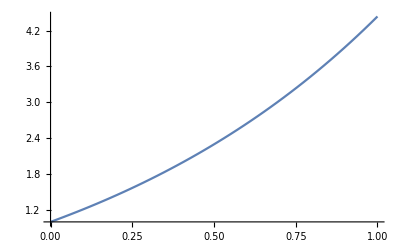

```mathematica
Plot[y[x]/.soln/.a->1,{x,0,1}]
```

We can solve a boundary value problem:

```mathematica
DSolve[{y''[x]==-Sin[x],y[0]==0,y[1]==0},y,x]
```

{{y→Function[{x},-x Sin[1]+Sin[x]]}}

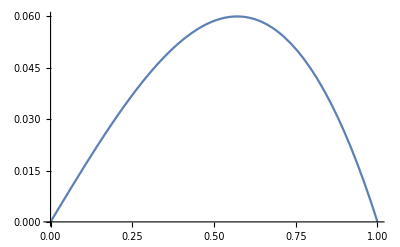

```mathematica
Plot[y[x]/.%,{x,0,1}]
```